## How to dig the data out of the waveform

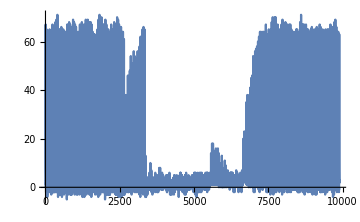
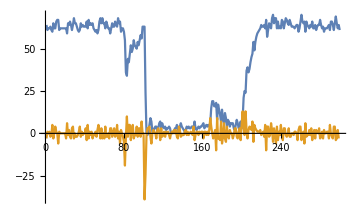

```mathematica
sampledataraw=Import["D:\\pcdata\\data3\\data6557___5_4.csv", "Table"][[50;; 9950, 1]]+33;
{ListLinePlot[sampledataraw, ImageSize->360, PlotRange->All],
ListLinePlot[{#, ListConvolve[{1, -1}, #]}&@Table[(Max@#+Min@#)&@(#[[1+33(k-1);;33k]])&@sampledataraw, {k, 300}], ImageSize->360, PlotRange->All]}
```

## Parse function

```mathematica
parseWave[raw_]:=Module[{wave, snap, offset, data, lophase, circphase, cal},
wave=N@Table[(Max@#+Min@#)&@(#[[1+33(k-1);;33k]])&@raw, {k, 300}];
snap=77+First@First@Position[#, Min@#]&@ListConvolve[{1, -1}, #]&@wave[[75;;85]];
offset=-Mean@Part[#, snap+55;;snap+64]&@wave;
(*wave=wave+offset;*)
data=wave[[snap+88]]+offset;
cal=offset+Take[wave, -50]//Mean;
lophase=ArcTan[cal, 64+Mean@(wave[[snap+24;;snap+28]])];
circphase=ArcTan[cal, 256+4Mean@(wave[[snap+36;;snap+44]])]-.4654lophase;
{data, lophase, circphase}
]
```

```mathematica
parseWave[Import["D:\\pcdata\\data3\\data6557___"<>ToString@(278)<>"_"<>ToString@1<>".csv"]]
```

{15.3,0.1014,0.016316}

## Generate files

### lv1

```mathematica
data12=Table[Import["D:\\pcdata\\data2\\data9157___"<>ToString@(i)<>"_"<>ToString@j<>".csv"][[;;, 1]], {i, 277}, {j, 10}];
data13=Table[Import["D:\\pcdata\\data3\\data6557___"<>ToString@(i)<>"_"<>ToString@j<>".csv"][[;;, 1]], {i, 277}, {j, 10}];
```

```mathematica
datalv1=Join[#[[1]], #[[2]], 2]&@Map[parseWave, {data12, data13}, {3}];
```

```mathematica
Export["data1a.mat", datalv1]
```

data1a.mat

### lv2

```mathematica
data23=Table[Import["D:\\pcdata\\data3\\data6557___"<>ToString@(i+277)<>"_"<>ToString@j<>".csv"][[;;, 1]], {i, 40}, {j, 10}];
data24=  Table[Import["D:\\pcdata\\data4\\data8491___"<>ToString@(i+277)<>"_"<>ToString@j<>".csv"][[;;, 1]], {i, 40}, {j, 10}];
data25=Table[Import["D:\\pcdata\\data5\\data9340___"<>ToString@(i+277)<>"_"<>ToString@j<>".csv"][[;;, 1]], {i, 40}, {j, 10}];
```

```mathematica
datalv2=Join[#[[1]], #[[2]], #[[3]], 2]&@Map[parseWave, {data23, data24, data25}, {3}];
```

```mathematica
Export["data2a.mat", datalv2]
```

data2a.mat

### lv3

```mathematica
data34=Table[Import["D:\\pcdata\\data4\\data8491___"<>ToString@(i+317)<>"_"<>ToString@j<>".csv"][[;;, 1]], {i, 1199}, {j, 10}];
```

```mathematica
datalv3=Map[parseWave, data34, {2}];
```

```mathematica
Export["data3a.mat", datalv3]
```

data3a.mat